# PX4514: Volleyball Setter Model

## Pawel Kaniowski and Sonke Wohler

## Initialisation and Model Definitions

This Group of instructions should be executed automatically upon opening the Notebook. 
It serves as the initialisation, defining constants and functions required by the Model.
essentially this is the “Under the Hood” Section.

```mathematica
CleanSlate[];ClearAll["Global`*"]; 
(* only the combination of these commands seems to completely clear the kernel, perhaps we are doing something wrong here.
Low Priority bug *)
```

### Constants for the Model

Note that constants, while near exclusively static values, may be defined as functions at times due to the limitations set out by the Mathematica programming language.

#### Coordinate System specs

We laid a coordinate system over the playing field in order to describe player positions independent of their position in the rotation.

-Graphics-

```mathematica
(* boundaries for the coordinate system *)
minX=1 ; maxX=13;
minY=1 ; maxY=9;
(* boundaries of the allowed playing field inside the coordinate system (players can contact the ball outside this area but only without toughing the ground) *)
startX=3 ; endX=11;
startY=1 ; endY=9;
(* translate coordinates to a decimal between 0 and 1 *)
getXScale[x_]=x/maxX;
getYScale[y_]=1-(y/maxY); (* y coordinates are reverse between our representation and mathematica image coordinates *)
```

#### Constants specific to each position

Here we used function definitions rather than lists in order to start indices from 0.
0 refers to the setter independent of their position, and in the case of attack to a “Dump” where the setter goes straight to the attack without setting to a position, while indices above 0 directly describe the player that is being set to.
player numbers describe their position inside the rotation, in accordance with volleyball standards.

```mathematica
(* ideal position to set from *) 
idealCoordinates[0]={8,1}; 
(* ideal position for player at position p to contact the ball at *)
idealCoordinates[1]={10,3}; 
idealCoordinates[2]={11,1};
idealCoordinates[3]={7,1};
idealCoordinates[4]={3,1};
idealCoordinates[5]={4,3};
idealCoordinates[6]={7,3};
```

```mathematica
(* basic assumed difficulty of a "Dump"*)
positionBias[0]=0.9;
(* basic assumed difficulty for a player at position p to attack successfully *)
positionBias[1]=0.5;
positionBias[2]=0.1;
positionBias[3]=0.3;
positionBias[4]=0.1;
positionBias[5]=1.0; (* this position cannot be set to, it is always occupied by a defence player *)
positionBias[6]=0.6;
(* note: while front court players tend to have lower success rates overall, they are set to more often as they are usually more likely to score successfully. *)
```

```mathematica
(* the setter's coordinates are dynamically defined by setterPosition *)
positionCoordinates[0]:=setterCoordinates;
(* the coordinates that a player at position p is assumed to start from when the ball is served *)
positionCoordinates[1]={11,6};
positionCoordinates[2]={9,1};
positionCoordinates[3]={9,1};
positionCoordinates[4]={3,1};
positionCoordinates[5]={4,2};
positionCoordinates[6]={8,2};
```

```mathematica
(* the coordinates that positions have as they are usually displayed *) 
displayCoordinates[1]={10,7};
displayCoordinates[2]={10,2};
displayCoordinates[3]={7,2};
displayCoordinates[4]={4,2};
displayCoordinates[5]={4,7};
displayCoordinates[6]={7,7};
```

```mathematica
(* this line allows this cell to be processed correctly *)
setterCoordinates={0,0};
(* determines whether the setter is allowed to set to a position or not *)
positionIsValid[0]:=setterCoordinates[[2]]≤1; (* "Dump" is only feasable very close to the net *)
positionIsValid[1]:=If[setterIsFrontCourt == True ,True,False];(* only allowed when the setter is front court *)
positionIsValid[2]:=If[setterIsFrontCourt == True ,False,True];(* only allowed when the setter is back court *)
positionIsValid[3]:=If[4>setterCoordinates[[2]]  && 5> distanceFromIdeal,True,False];(* Position 3 is only feasable if the setter s very close, otherwise the opposing team will "gang up" in the time they have to react *)
positionIsValid[4]=True;(* always allowed *)
positionIsValid[5]=False;(* This position is occupied by a defence player and cannot be set to *)
positionIsValid[6]=True; (* always allowed *)
```

```mathematica
(* These lists are used for display purposes *)
scaleXList=Table[getXScale[displayCoordinates[i][[1]]],{i,6}];
scaleYList=Table[getYScale[displayCoordinates[i][[2]]],{i,6}];
```

#### Scale quantities by their expected maximum

Lastly, throughout the model it proved useful to use relative values by scaling factors and terms relative to their maximum possible value.

```mathematica
scaleFactor[max_,quant_]:=1-(quant/max);
```

```mathematica
maxDistance=EuclideanDistance[{endX,endY},{startX,startY}];
```

```mathematica
(* The maximum difficulty that can be assigned by 'positionSetDifficulty'*)
maxSetDifficulty=17;
```

```mathematica
maxPressure=23;
```

```mathematica
maxRun=EuclideanDistance[positionCoordinates[1],{minX,minY}];
```

```mathematica
maxDifficulty=1;
```

```mathematica
(* the assumed maximum number of plays  *)
maxSettings=100;
```

```mathematica
(* for final positionScores *)
 maxPositionScore=maxPressure*(1+1);
```

### Functional Decelerations

The functional specifications of the Model begin here. These translate to Mathematical functions as also described in the Project Report.

#### Functions without Parameters

These functions are unspecific to any particular player and change only when game parameters change i.e. when a point is scored.

```mathematica
(* the amount of pressure the players feel due to the game state *)
pressure:=Max[(oponentsPoints-ownPoints)*Min[Max[ownPoints,oponentsPoints]/25,1] ,0]+1;
```

```mathematica
(* how far the setter is from the ideal setting position *)
distanceFromIdeal:=EuclideanDistance[setterCoordinates,idealCoordinates[0]];
```

```mathematica
(* how comfortably the setter could reach the ball from their position *)
distanceToRun:=EuclideanDistance[positionCoordinates[setterPosition],setterCoordinates];
```

```mathematica
(* whether the setter is in front court (=True) or back court (=False) *)
setterIsFrontCourt:=MemberQ[{2,3,4},setterPosition];
```

```mathematica
(* describes the difficulty the setter has to contact the ball, reducing the quality of the set *)
easeOfSet:=scaleFactor[maxDistance,distanceFromIdeal];
```

#### Parameterized Functions based on Player Positions

These Functions evaluate and usually score some properties of individual players on the playing field.

```mathematica
(* converts positionIsValid[p] to a number *)
positionValidityFactor[p_Integer]:=If[positionIsValid[p] ,1,0];
```

```mathematica
(* how far the setter would have to throw to set to position p from their current coordinates *)
distanceToThrow[p_Integer ]:=EuclideanDistance[ setterCoordinates,idealCoordinates[p]];
```

```mathematica
(* score position p by how likely the setter is to set to it well *)
setToScore[p_Integer]:=scaleFactor[maxSetDifficulty,distanceToThrow[p]];
```

```mathematica
(* score a position p by how likely the player is to attack successfully *)
attackerScore[p_Integer]:=scaleFactor[maxDifficulty,positionBias[p]];
```

```mathematica
(* score a position p by how likely the setter may be to set to it *)
positionScore[p_]:=  positionValidityFactor[p]*(setToScore[p]+easeOfSet*pressure*attackerScore[p]);
```

#### Top Level

These Functions are intended to ease usage of the Model or allow atomisation of it.
By enlarge each one produces a list of scores that can be accessed globally, based on global variables defined in the sections above.

```mathematica
(* score all positions based on the already defined input values *)
calculateAllScores:=listOfScores=Table[positionScore[p],{p,0,6}];
```

```mathematica
(* use preveously calculated scores and convert them to percentage values *)
convertScoresTopercentages:=percentageScores=listOfScores/Total[listOfScores];
```

```mathematica
(* sort previously calculated scores in descending order *)
orderScores:=orderOfScores=Reverse[Ordering[percentageScores]]/.x_->(x-1);
```

```mathematica
(* perform the last three operations in order *)
fullCalculate:=(calculateAllScores;convertScoresTopercentages;orderScores;);
```

```mathematica
(* set input values *)
setInputs[ownPointsIn_Integer,oponentsPointsIn_Integer,setterPositionIn_Integer,setterCoordinatesIn_List]:=(
ownPoints=ownPointsIn;
oposingPoints=oponentsPointsIn;
remainingSets=remainingSetsIn;
setterCoordinates=setterCoordinatesIn;
)
```

### Initialise with some Default Input Variables

These are examples of the required inputs that are used as default in case the functions are called without these having been initialized. Hence any unexpected outputs or errors are cause by bugs or failure to run initialisation entirely, rather than forgetting to define input values. This is mostly useful for development and testing.

```mathematica
(* the current score for our team *)
ownPoints=0;
```

```mathematica
(* the current score for the opposing team *)
oponentsPoints=0;
```

```mathematica
(* the position inside the rotation that the setter is in *)
setterPosition=1;
```

```mathematica
(* the coordinates on the field that the setter contacts the ball at *)
setterCoordinates={9,2};
```

```mathematica
(* initialise listOfScores as well *)
fullCalculate;
```

### Preparing Images and similar for Visualisation

These images are used for visualisation purposes, and may only be relevant for the presentation.

```mathematica
(* A decent image from https://www.strength-and-power-for-volleyball.com/volleyball-court.html *)
fieldImage=-Graphics-;
```

```mathematica
(* An image of the coordinate system we use *)
excelFieldImage=-Graphics-;
```

```mathematica
(* These frames are used to mark positions on image *)
redFrame=-Graphics-; (*  *)
blueFrame=-Graphics-; (* *)
```

```mathematica
(* by resizing the fieldImage we can use scaleXList and scaleYList to display scores in the correct positions on image *)
fieldDisplayImage=ImageResize[fieldImage,ImageDimensions[excelFieldImage]];
```

```mathematica
(* display the scores calculated by the model after they have been calculated 
note that this may take some processing *) 
displayCurrentScores:=(
maxScorePosition=orderOfScores[[1]];
displayImage=fieldDisplayImage;
For[i=1,i<7,i++,
text=percentageScores[[i]];
graphs=Graphics[ Text[ text ] ];
scale={ scaleXList[[i]],scaleYList[[i]] };
displayImage=ImageCompose[displayImage,graphs,Scaled[scale]];
If[i==maxScorePosition,
graphs=ImageCompose[Graphics[ImageGraphics[redFrame]],graphs];
displayImage=ImageCompose[displayImage,graphs,Scaled[scale]];
,
Indeterminate;
];
If[i==realSetterChoice,
graphs=ImageCompose[Graphics[ImageGraphics[blueFrame]],graphs];
displayImage=ImageCompose[displayImage,graphs,Scaled[scale]];
,
Indeterminate;
];
];
graphs=Graphics[ Text[ Style["X" ,Bold,Blue,Magnification->1.5] ]];
scale={getXScale[setterCoordinates[[1]]],getYScale[setterCoordinates[[2]]+0.5]};
displayImage=ImageCompose[displayImage,graphs,Scaled[scale]];)
```

### Functions for iterating over real match Data

This is how we can compare the Model to real Data from a Match. 
This is what is referred to by “automation” when mentioned in the above functions.

```mathematica
(* an example Dataset from a real match to compare the model to *)
ownPointsList={2,2,3,3,3,6,8,9,10,11,14,15,17,18,18,19,19,20,23,23,23,25};
oponentsPointsList={2,3,4,4,5,6,7,8,9,10,12,13,14,15,16,16,16,17,21,23,24,25};
setterPositionList={1,1,6,6,6,5,4,3,2,1,5,4,3,2,2,1,1,1,5,5,5,3};
setterCoordinateList={{5,3},{6,5},{7,1},{7,2},{8,5},{7,3},{6,5},{10,3},{5,1},{7,3},{8,2},{8,2},{9,5},{7,1},{6,2},{8,4},{8,2},{12,6},{5,3},{7,3},{7,4},{10,2}};
setToList={2,4,3,4,2,2,4,1,3,2,0,6,1,4,4,4,2,6,4,2,4,3};
(* these lists are 22 entries long *)
```

```mathematica
(* Helps iterate over example Dataset *)
getFromLists[i_Integer]:=(
ownPoints=ownPointsList[[i]];oponentsPoints=oponentsPointsList[[i]];setterPosition=setterPositionList[[i]];setterCoordinates=setterCoordinateList[[i]];
realSetterChoice=setToList[[i]];
)
```

```mathematica
(* iterate over example Data and produce a List of Scores based on its inputs, as well as an oredering of the best to worst Scored Positions *)
iterateOverLists:=(
listLength=Length[ownPointsList];positionScoreList=Range[listLength];positionOrderList=Range[listLength];realChoiceRankList=Range[listLength];
choiceRankCount=Table[0,{i,1,7}];
positionRankCount=Table[Table[0,{i,1,7}],{j,1,7}];
For[i=1,i<listLength+1,i++,
getFromLists[i];
calculateAllScores;
convertScoresTopercentages;
positionScoreList[[i]]=percentageScores;
orderScores;
positionOrderList[[i]]=orderOfScores;
realChoiceRank=Position[orderOfScores,setToList[[i]]][[1]][[1]];
realChoiceRankList[[i]]=realChoiceRank;
choiceRankCount[[realChoiceRank]]++;
positionRankCount[[setToList[[i]]+1]][[realChoiceRank]]++;
];
)
```

This produces the following lists that can be used to evaluate the Model.

```mathematica
(* For each 'cycle' a list of the scores that have been assigned to each position of the format {"Dump", 1, 2, ...} *)
positionScoreList
```

```mathematica
(* For each 'cycle' a ranking of the positions, from highest to lowest score *)
positionOrderList
```

```mathematica
(* A list of how highly scored the real setter's decision was by the system *)
realChoiceRankList
```

```mathematica
(* A count of how often the real setter's choice was scored {highest, second highest, etc.} by the model *) 
choiceRankCount
```

```mathematica
(* A list for how often this position (index - 1) was scored {highest, second highest, etc. } by the model independent of the real setter's choices *)
positionRankCount
```

## Short Description of the Model

The following variables are used to run the Model:

```mathematica
ownPoints=5(* how many points we scored so far *);
oponentsPoints=10  (* this puts us 5 points behind *);
setterPosition=2 (* the position within the player rotation that the setter is currently occupying *);
setterCoordinates= {8,1} (* the playing field coordinates on which the setter has come into contact with the ball *);
```

The Model calculates a score for each player by the position they occupy, for example player 3:

```mathematica
positionScore[3]
```

3.04118

This scores the likelihood of the setter to set the ball to this position based on the difficulty to do so and the chances that this will lead to scoring a point against the opponent.

```mathematica
?? positionScore
```

Global`positionScore

positionScore[p_]:=positionValidityFactor[p] (setToScore[p]+easeOfSet pressure attackerScore[p])

Positions that cannot be set to, or that never are in game, are scored with 0 by the `positionValidityFactor`

Furthermore, `setToScore` describes the difficulty for the setter to set to a particular position.

`easeOfSet` describes how difficult it was for the setter to still contact the ball and perform a successful set. The assumption being that the harder this was the more the setter will focus on choosing a position that they will still be able to successfully set to, and reducing the relevance of the `attackerScore`.

The `attackerScore` simply describes a bias to choose certain positions. For the most part positions closer to the net are more promising as they give the opponent less time to react, while the centre position does so extremely well as long as the setter is close enough.

Lastly, the `pressure` a player is under is set based on the current state of the game.

You can calculate the scores for all players by executing `calculateAllScores`.

```mathematica
calculateAllScores
```

{1.3,2.33362,0.,3.04118,3.40588,0.,2.06847}

The first return value refers to something called “Dump”, when the setter does not set to any other player but instead attacks directly.
Then the players are scored in order from 1 to 6. Note that position 5 is not allowed and that the setter cannot set to themselves.

We can further refine these scores by displaying them as fractions.

```mathematica
convertScoresTopercentages
```

{0.107003,0.192081,0.,0.25032,0.280339,0.,0.170256}

But more importantly, we can order the positions by their scores.
“0” here refers to the “Dump”, other numbers to player positions.

```mathematica
orderScores
```

{4,3,1,6,0,5,2}

This means that, given the above defined inputs, our model predicts that positions 4 and  3 are likely to be the best choices, while position 1 may or may not be a decent choice and most other positions would be a bad choice.

It should be noted that if a setter would always choose the ideal position (here 4)  their choices would become rather predictable, which would increase the chances for the opposing team to react and successfully defend against an attack. Hence, while position 4 is considered the best choice, the setter is still likely to choose position 3 instead in order to be less predictable.
While the choice of 3 over 4 is by no means truly random, it is a humanly random decision that we may not be able to model very accurately, even if we decide to expand the model to include this aspect in the future.
This obviously is a significant drawback to the model, as we cannot be certain at this time whether a setter choosing position 3 in this case is because of this human randomness or if it is an error in our model.

## Comparing the Model to Real Data

Making use of the Model we can take in Data from a real Match, or multiple matches, and attempt to compare our predictions to the Match in order to evaluate the Model.

Below is an example data set from a real match which we want to evaluate with our model. The lists are 22 entries long.

```mathematica
ownPointsList={2,2,3,3,3,6,8,9,10,11,14,15,17,18,18,19,19,20,23,23,23,25};
oponentsPointsList={2,3,4,4,5,6,7,8,9,10,12,13,14,15,16,16,16,17,21,23,24,25};
setterPositionList={1,1,6,6,6,5,4,3,2,1,5,4,3,2,2,1,1,1,5,5,5,3};
setterCoordinateList={{5,3},{6,5},{7,1},{7,2},{8,5},{7,3},{6,5},{10,3},{5,1},{7,3},{8,2},{8,2},{9,5},{7,1},{6,2},{8,4},{8,2},{12,6},{5,3},{7,3},{7,4},{10,2}};
setToList={2,4,3,4,2,2,4,1,3,2,2,6,1,4,4,4,2,6,4,2,4,3};
```

With Data setup like this we can iterate over it and compare the Model predictions against the decisions of the real setter(s) with this function:

```mathematica
iterateOverLists;
```

```mathematica
?? iterateOverLists
```

Global`iterateOverLists

iterateOverLists:=(listLength=Length[ownPointsList];positionScoreList=Range[listLength];positionOrderList=Range[listLength];realChoiceRankList=Range[listLength];choiceRankCount=Table[0,{i,1,7}];positionRankCount=Table[Table[0,{i,1,7}],{j,1,7}];For[i=1,i<listLength+1,i++,getFromLists[i];calculateAllScores;convertScoresTopercentages;positionScoreList⟦i⟧=percentageScores;orderScores;positionOrderList⟦i⟧=orderOfScores;realChoiceRank=Position[orderOfScores,setToList⟦i⟧]⟦1⟧⟦1⟧;realChoiceRankList⟦i⟧=realChoiceRank;choiceRankCount⟦realChoiceRank⟧++;positionRankCount⟦setToList⟦i⟧+1⟧⟦realChoiceRank⟧++;];)

At each iteration we produce a list of scores, based on which we order the possible choices that the setter can make, as described in the previous section. This is temporarily stored in orderOfScores:

```mathematica
orderOfScores
```

{3,1,4,6,5,2,0}

As part of the inputs we have the decision the real setter made in our real world example, stored in realSetterChoice, as retrieved from setToList above.

```mathematica
realSetterChoice
```

3

We can illustrate this on the field.

```mathematica
displayCurrentScores;
displayImage
```

-Graphics-

As you can see, in the last iteration the real decision the setter made corresponded to our model prediction. In other words realSetterChoice was our model’s first choice.

How often realSetterChoice was the model’s first, second, third, etc. choice is recorded in the choiceRankCount list.

```mathematica
choiceRankCount
```

{13,7,1,1,0,0,0}

For this data set our model appears to predict the setter’s decisions rather well. In a simple graph this looks like this:

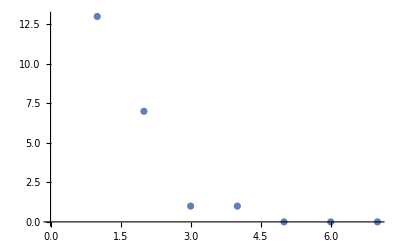

```mathematica
ListPlot[choiceRankCount]
```

While iterating over the inputs the model also records this parameter separately for each position in positionRankCount, which allows us to plot the above graph for each position.

```mathematica
positionRankCount
```

{{0,0,0,0,0,0,0},{2,0,0,0,0,0,0},{3,3,1,0,0,0,0},{2,1,0,0,0,0,0},{6,2,0,0,0,0,0},{0,0,0,0,0,0,0},{0,1,0,1,0,0,0}}

For example for Position 2

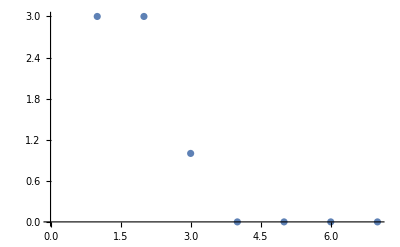

```mathematica
ListPlot[positionRankCount[[3]]]
```

Position 3

```mathematica
ListPlot[positionRankCount[[3]]]
```

-Graphics-

Position 4

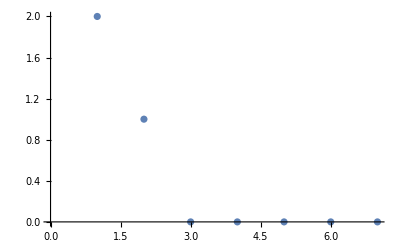

```mathematica
ListPlot[positionRankCount[[4]]]
```

## A Debugging Example

Debugging is perhaps more important in programming than the ability to produce sensible ideas. As part of this Project we have stumbled into many dead-ends, too many to illustrate. However below is one example that on the one hand illustrates some of our problems getting used to Mathematica, and on the other hand perhaps shows something about our Model.

We attempted to run the Model on an example set while some of our functions were defined in the following way:

```mathematica
(* using this function we wanted to retrieve elements from the below lists *)
getFromLists[i_Integer]:=ownPoints=ownPointsList[[i]];oponentsPoints=oponentsPointsList[[i]];setterPosition=setterPositionList[[i]];setterCoordinates=setterCoordinateList[[i]];
(* which was used here to iterate over said lists *)
iterateOverLists:=listLength=Length[ownPointsList];positionScoreList=Range[listLength];positionOrderList=Range[listLength];realChoiceRankList=Range[listLength];For[i=1,i<listLength+1,i++,
getFromLists[i];
calculateAllScores;
convertScoresTopercentages;
positionScoreList[[i]]=percentageScores;
orderScores;
positionOrderList[[i]]=orderOfScores;
realChoiceRankList[[i]]=Position[orderOfScores,setToList[[i]]][[1]][[1]];
];
```

```mathematica
(* the aforementioned lists from a real match *)
ownPointsList={2,2,3,3,3,6,8,9,10,11,14,15,17,18,18,19,19,20,23,23,23,25};
oponentsPointsList={2,3,4,4,5,6,7,8,9,10,12,13,14,15,16,16,16,17,21,23,24,25};
setterPositionList={1,1,6,6,6,5,4,3,2,1,5,4,3,2,2,1,1,1,5,5,5,3};
setterCoordinateList={{5,3},{6,5},{7,1},{7,2},{8,5},{7,3},{6,5},{10,3},{5,1},{7,3},{8,2},{8,2},{9,5},{7,1},{6,2},{8,4},{8,2},{12,6},{5,3},{7,3},{7,4},{10,2}};
setToList={2,4,3,4,2,2,4,1,3,2,0,6,1,4,4,4,2,6,4,2,4,3};
(* the set is 22 entries long *)
```

Here is what the model produced:

```mathematica
iterateOverLists;
realChoiceRankList
```

{4,2,1,2,4,4,2,6,1,4,7,3,6,2,2,2,4,3,2,4,2,1}

```mathematica
choiceRankCount
```

{2,8,2,6,0,2,1}

That doesn’t look that bad for an early implementation. But when the setter’s choice was ranked 6th at 8, 11 and 13 we got curious.

```mathematica
setToList[[8]]
setToList[[11]]
setToList[[13]]
```

1

0

1

Seemingly we score position 1 unexpectedly badly, in fact we consider it always invalid

```mathematica
positionScoreList
```

{{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691},{0.,0.,0.240446,0.260077,0.252786,0.,0.246691}}

Trying to recreate this situation it becomes obvious: getFromLists does not set setterPosition at all

```mathematica
getFromLists[8]
setterPositionList[[8]]
setterPosition
```

9

3

1

In fact it only sets the initial value, ownPoints

```mathematica
getFromLists[8]
ownPoints
ownPointsList[[8]]
oponentsPoints
oponentsPointsList[[8]]
setterPosition
setterPositionList[[8]]
setterCoordinates
setterCoordinateList[[8]]
```

9

9

9

2

8

1

3

{5,3}

{10,3}

Hence our “not so bad” Data was actually only Data from one position and one set of values always producing the same output.

```mathematica
positionOrderList
```

{{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0}}

Perhaps this is because our default values are very well chosen and represent a significant portion of the expected outcomes rather well.

```mathematica
positionOrderList
```

{{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,0,1,4,2,6,5},{3,1,4,2,6,5,0},{3,1,4,2,6,5,0},{3,1,4,6,2,5,0},{3,1,6,2,5,4,0},{1,4,2,6,5,3,0},{3,4,0,1,6,5,2},{3,4,6,2,5,1,0},{3,1,4,6,2,5,0},{3,1,6,2,5,4,0},{1,4,6,2,5,3,0},{3,0,1,4,6,5,2},{3,4,1,6,5,2,0},{3,4,6,2,5,1,0},{3,4,6,2,5,1,0},{3,4,2,6,5,1,0},{3,4,1,6,2,5,0},{3,1,4,6,2,5,0},{3,1,4,6,2,5,0},{1,4,2,6,5,3,0}}

In the end our problem was that we defined multi-expression functions, but left out the brackets. Hence only the first expression of each function actually executed when evaluating it, such that the model was evaluated repeatedly on the same values.

## Full Data Set Comparison

Above we illustrated how we compared real world data to our model outputs. However, the data used for demonstration has only been much like a training set, to inform development, debug the code and adjust biases to sensible values.
Below we use a much larger test data set to evaluate model performance.

First we import the data and run the model.

```mathematica
inputList=ReadList[FileNameJoin[{NotebookDirectory[],"data.txt"}],Number,RecordLists->True];
inputLength=Length[inputList];
ownPointsList=Table[inputList[[i]][[1]],{i,1,inputLength}];
oponentsPointsList=Table[inputList[[i]][[2]],{i,1,inputLength}];
setterPositionList=Table[inputList[[i]][[3]],{i,1,inputLength}];
setterCoordinateList=Table[{inputList[[i]][[4]],inputList[[i]][[5]]},{i,1,inputLength}];
setToList=Table[inputList[[i]][[6]],{i,1,inputLength}];
```

```mathematica
iterateOverLists;
choiceRankCount
```

{51,35,18,6,0,0,0}

A quick plot shows that, by enlarge, the model is right more often than wrong.

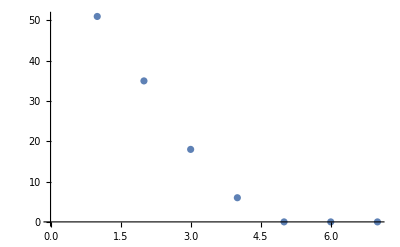

```mathematica
ListPlot[choiceRankCount]
```

While this looks quite compelling, we can perform regression over this.
Because there are normally two positions that the setter cannot set to (position 5 and their own position) we can ignore the last two points on this list and limit regression to the first 4 points.

```mathematica
regression=LinearModelFit[Table[choiceRankCount[[i]],{i,1,4}],x,x]
```

FittedModel[65.5-15.2 x]

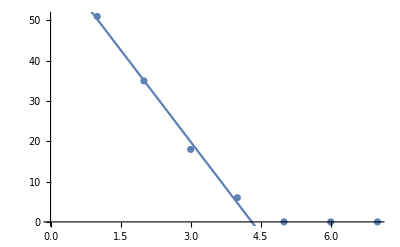

```mathematica
ListPlot[choiceRankCount]~Show~Plot[regression["BestFit"],{x,0,7}]
```

```mathematica
regression["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 65.5 | 2.08567 | 31.4048 | 0.00101239
x | -15.2 | 0.761577 | -19.9586 | 0.00250097

Hence, we can reject the null hypothesis at the 1% margin and confidently say that sets that are scored highly by the model are likely to be chosen by the setter.

## Other Figures Used for the Report

If applicable, below are any figures and tables created solely for the report and not already created in the previous sections.